## Cancel a constant disturbance using a disturbance estimator (Ch. 4, Example 4.14)

```mathematica
Clear["Global`*"]                                              (* clear everything *)
```

```mathematica
M0 = ({{s+1+k+l, 0}, {ld, s}});M0inv = Inverse[M0];  MatrixForm[M0inv] //Simplify
```

(1/(1+k+l+s) | 0
-ld/(s (1+k+l+s)) | 1/s)

```mathematica
Guy =  ({{k, 1}}).( M0inv .({{l}, {ld}})) // Simplify;  Guy
```

{{(k l s+ld (1+k+s))/(s (1+k+l+s))}}

```mathematica
bigA = ({{-1, 1, -k, -1}, {0, 0, 0, 0}, {l, 0, -(1+k+l), 0}, {ld, 0, -ld, 0}}) /.k-> 1/.l-> 2/.ld-> 2 ;
```

```mathematica
bigB = ({{0}, {0}, {0}, {0}}); (* no inputs *)
```

```mathematica
sys0 = StateSpaceModel[{bigA,bigB}]  (* only need dynamics & input coupling matrices *)
```

-11-1-100000020-40020-200StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1-441FalseFalseFalseAutomaticNoneAutomatic

```mathematica
xout0 = StateResponse[{sys0,{0,1,0,0}},0,t] // Simplify
```

{ⅇ^(-2 t) (-3+3 ⅇ^t-2 t),1,2 ⅇ^(-2 t) (-1+ⅇ^t-t),ⅇ^(-2 t) (-1+ⅇ^t)^2}

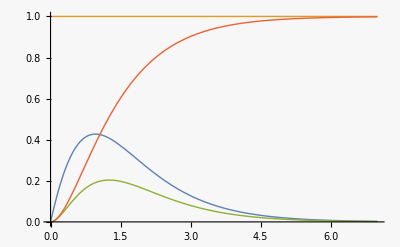

```mathematica
Plot[xout0,{t,0,7}]
```